# Retrato fase 2D

El sistema


tiene un solo punto de equilibrio en el origen.

Clasifica al punto de equilibrio.

Calculamos la matriz Jacobiana

```mathematica
J={{D[-3*x,x],D[-3*x,y]},{D[-8*x^2+1*y,x],D[-8*x^2+1*y,y]}}
```

{{-3,0},{-16 x,1}}

Evaluamos en el origen

```mathematica
TraditionalForm[J/.{x->0,y->0}]
```

(-3 | 0
0 | 1)

La matriz es diagonal, por lo que los eigenvalores son los elementos en la diagonal. Un eigenvalor es negativo y otro es positivo, por lo que tenemos un punto silla. Equivalentemente, el determinante es negativo, lo que también indica un punto silla.

Encuentra la solución exacta del sistema con condiciones iniciales , .

La primera ecuación está desacoplada y es lineal, por lo que podemos encontrar la solución de manera trivial como . Necesitamos usar la condición inicial . Sustituyendo en la solución encontramos que , por lo que la solución particular con condiciones iniciales es .
Sustituimos esta solución en la segunda ecuación y encontramos la ecuación lineal inhomogénea

Esta la podemos resolver ya sea con factor integrante o como combinación lineal de la homogénea más una particular de la inhomogénea. Usando factor integrante tenemos:

El factor integrante es , multiplicamos de ambos lados y obtenemos






Usamos la condición inicial  y obtenemos


Sustituyendo obtenemos la solución


Por lo que la solución al sistema son las funciones

Usando las soluciones, encuentra el lugar geométrico de las condiciones iniciales  en el espacio fase tal que las soluciones tienden al punto de equilibrio en el límte . Ésta es la variedad estable.

El punto de equilibrio es el origen, por lo que necesitamos encontrar  tales que  y .
Vemos que, sin importar el valor de , siempre se cumple que . Por otro lado,  por lo general diverge, excepto si el coeficiente de  es cero. Por lo tanto, tenemos que  sólo si , es decir si 
.
El lugar geométrico en el espacio fase de estas condiciones iniciales es una parábola unitaria con vértice en el origen.

Usando las soluciones, encuentra el lugar geométrico de las condiciones iniciales  en el espacio fase tal que las soluciones tienden al punto de equilibrio en el límte . Ésta es la variedad inestable.

En este caso, tenemos que encontrar  tales que  y . En este caso vemos que  diverge en este límite excepto si es cero para toda . Esto sólo se cumple si .  también diverge en general, excepto cuando el coeficiente de  es cero, es decir, cuando  también. Es decir, el lugar geométrico de condiciones iniciales en el espacio fase que tienden al punto de equilibrio en el límite especificado es la recta vertical .

Comprueba las respuestas de los dos incisos anteriores graficando el retrto fase e indicando las variedades estables e inestables.

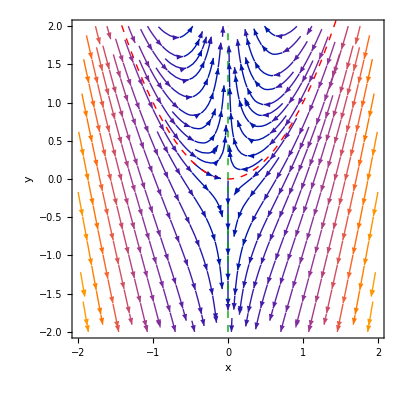

```mathematica
Show[{StreamPlot[{-3*x,-8x^2+2*y},{x,-2,2},{y,-2,2},FrameLabel->{x,y},Epilog->{Directive[{Thick,Darker[Green],Dashed}],Line[{{0,-2},{0,2}}]}],Plot[x^2,{x,-2,2},PlotStyle->{Red,Thick,Dashed}]}]
```

La línea roja es la variedad stable, y la línea verde es la variedad inestable.

Describe el comportamiento de las soluciones en el límite  para cualquier condición inicial arbitraria.

Como vimos anteriormente, las soluciones con condiciones iniciales sobre la parábola unitaria tienden al origen en este límite. Como vemos gracias a las soluciones explícitas, todas las soluciones cumplen que , por lo que todas las soluciones tienden al eje . Finalmente, viendo las solución explícita de  vemos que, con excepción de la variedad estable, las soluciones sobre la parábola (aquellas con ) cumplen que , mientras que aquellas debajo de la parábola (con ), cumplen que .